Damian Słota
Katedra Zastosowań Matematyki i Metod Sztucznej Inteligencji
Wydział Matematyki Stosowanej
Politechnika Śląska

# Dwufazowe zagadnienie Stefana

## Przykład 1 (topienie)

### Zwykłe pochodne

```mathematica
Clear[u1,u2,s,a1,a2,t,x,kappa,λ1,λ2,pl,pp];
```

```mathematica
u1[x_,t_]:=Exp[a1*t-x];
u2[x_,t_]:=Exp[a2*t-x];
s[t_]:=a1*t
```

Obszar: x ∈ [0, 2], t ∈ [0, 2]

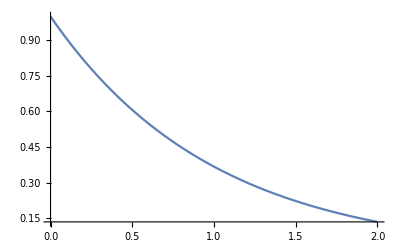

```mathematica
Plot[u1[x,0]/.{a1->1},{x,0,2}]
```

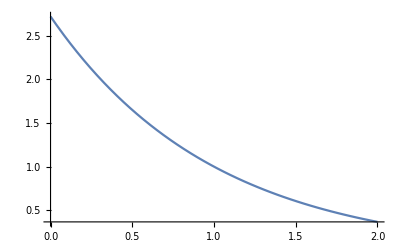

```mathematica
Plot[u1[x,1]/.{a1->1},{x,0,2}]
```

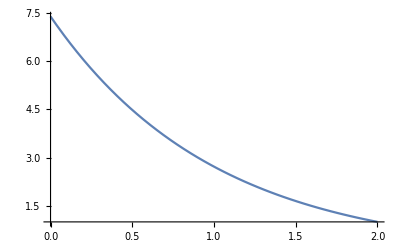

```mathematica
Plot[u1[x,2]/.{a1->1},{x,0,2}]
```

Warunek a1 = a2

Równanie przewodnictwa w fazie 1 (ciekłej)

```mathematica
a1*D[u1[x,t],{x,2}]-D[u1[x,t],t]
```

0

Równanie przewodnictwa w fazie 2 (stałej)

```mathematica
a2*D[u2[x,t],{x,2}]-D[u2[x,t],t]
```

0

Warunek początkowy

```mathematica
u2[x,0]
```

ⅇ^-x

Warunek brzegowy pierwszego rodzaju dla x=0

```mathematica
u1[0,t]
```

ⅇ^(a1 t)

Warunek brzegowy pierwszego rodzaju dla x=2

```mathematica
u2[2,t]
```

ⅇ^(-2+a2 t)

Warunek ciągłości temperatury na granicy faz

```mathematica
u1[s[t],t]
```

1

Warunek a2 = a1

```mathematica
a2=a1
```

a1

```mathematica
u2[s[t],t]
```

1

Warunek Stefana

```mathematica
pl=-λ1*(D[u1[x,t],x]/.{x->s[t]})+λ2*(D[u2[x,t],x]/.{x->s[t]})
```

λ1-λ2

```mathematica
pp=D[s[t],t]
```

a1

```mathematica
kappa=pl/pp
```

(λ1-λ2)/a1

### Pochodna Caputo po czasie, α=1/2

```mathematica
Clear[u1,u2,s,a1,a2,t,x,kappa,λ1,λ2,pl,pp];
```

```mathematica
u1[x_,t_]:=Exp[a1*t-x];
u2[x_,t_]:=Exp[a2*t-x];
s[t_]:=a1*t
```

Obszar: x ∈ [0, 2], t ∈ [0, 2]

Rząd pochodnej ułamkowej

```mathematica
α=1/2;
```

Warunek a1 = a2

Równanie przewodnictwa w fazie 1 (ciekłej)

```mathematica
a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

a1 ⅇ^(a1 t-x)-√a1 ⅇ^(a1 t-x) Erf[√(a1 t)]

```mathematica
f1[x_,t_]:=-(a1 ⅇ^(a1 t-x)-√a1 ⅇ^(a1 t-x) Erf[√(a1 t)])
```

```mathematica
f1[x,t]+a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Równanie przewodnictwa w fazie 2 (stałej)

```mathematica
a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

a2 ⅇ^(a2 t-x)-√a2 ⅇ^(a2 t-x) Erf[√(a2 t)]

```mathematica
f2[x_,t_]:=-(a2 ⅇ^(a2 t-x)-√a2 ⅇ^(a2 t-x) Erf[√(a2 t)])
```

```mathematica
f2[x,t]+a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Warunek początkowy

```mathematica
u2[x,0]
```

ⅇ^-x

Warunek brzegowy pierwszego rodzaju dla x=0

```mathematica
u1[0,t]
```

ⅇ^(a1 t)

Warunek brzegowy pierwszego rodzaju dla x=2

```mathematica
u2[2,t]
```

ⅇ^(-2+a2 t)

Warunek ciągłości temperatury na granicy faz

```mathematica
u1[s[t],t]
```

1

Warunek a2 = a1

```mathematica
a2=a1
```

a1

```mathematica
u2[s[t],t]
```

1

Warunek Stefana

```mathematica
pl=-λ1*(D[u1[x,t],x]/.{x->s[t]})+λ2*(D[u2[x,t],x]/.{x->s[t]})
```

λ1-λ2

```mathematica
pp=1/Gamma[1-α] Integrate[(D[s[t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

(2 a1 √t)/(√π)

```mathematica
kappa=pl/pp
```

(√π (λ1-λ2))/(2 a1 √t)

### Pochodna Caputo po czasie, α=0.8

```mathematica
Clear[u1,u2,s,a1,a2,t,x,kappa,λ1,λ2,pl,pp];
```

```mathematica
u1[x_,t_]:=Exp[a1*t-x];
u2[x_,t_]:=Exp[a2*t-x];
s[t_]:=a1*t
```

Obszar: x ∈ [0, 2], t ∈ [0, 2]

Rząd pochodnej ułamkowej

```mathematica
α=8/10;
```

Warunek a1 = a2

Równanie przewodnictwa w fazie 1 (ciekłej)

```mathematica
a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

a1 ⅇ^(a1 t-x)-(a1^(4/5) ⅇ^(a1 t-x) (Gamma[1/5]-Gamma[1/5,a1 t]))/Gamma[1/5]

```mathematica
f1[x_,t_]:=-(a1 ⅇ^(a1 t-x)-(a1^(4/5) ⅇ^(a1 t-x) (Gamma[1/5]-Gamma[1/5,a1 t]))/Gamma[1/5])
```

```mathematica
f1[x,t]+a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Równanie przewodnictwa w fazie 2 (stałej)

```mathematica
a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

a2 ⅇ^(a2 t-x)-(a2^(4/5) ⅇ^(a2 t-x) (Gamma[1/5]-Gamma[1/5,a2 t]))/Gamma[1/5]

```mathematica
f2[x_,t_]:=-(a2 ⅇ^(a2 t-x)-(a2^(4/5) ⅇ^(a2 t-x) (Gamma[1/5]-Gamma[1/5,a2 t]))/Gamma[1/5])
```

```mathematica
f2[x,t]+a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Warunek początkowy

```mathematica
u2[x,0]
```

ⅇ^-x

Warunek brzegowy pierwszego rodzaju dla x=0

```mathematica
u1[0,t]
```

ⅇ^(a1 t)

Warunek brzegowy pierwszego rodzaju dla x=2

```mathematica
u2[2,t]
```

ⅇ^(-2+a2 t)

Warunek ciągłości temperatury na granicy faz

```mathematica
u1[s[t],t]
```

1

Warunek a2 = a1

```mathematica
a2=a1
```

a1

```mathematica
u2[s[t],t]
```

1

Warunek Stefana

```mathematica
pl=-λ1*(D[u1[x,t],x]/.{x->s[t]})+λ2*(D[u2[x,t],x]/.{x->s[t]})
```

λ1-λ2

```mathematica
pp=1/Gamma[1-α] Integrate[(D[s[t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

(5 a1 t^(1/5))/Gamma[1/5]

```mathematica
kappa=pl/pp
```

((λ1-λ2) Gamma[1/5])/(5 a1 t^(1/5))

## Przykład 2 (topienie, ale z drugiej strony)

### Zwykłe pochodne

```mathematica
Clear[u1,u2,s,a1,a2,t,x,kappa,λ1,λ2,pl,pp];
```

```mathematica
u1[x_,t_]:=Exp[a1*t+x-1];
u2[x_,t_]:=Exp[a2*t+x-1];
s[t_]:=1-a1*t
```

Obszar: x ∈ [0, 1], t ∈ [0, 1]

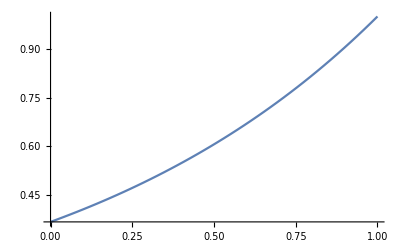

```mathematica
Plot[u1[x,0]/.{a1->1},{x,0,1}]
```

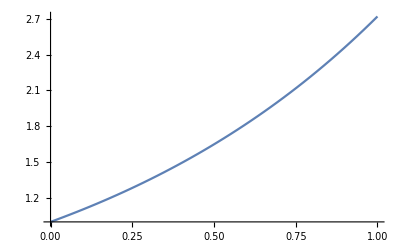

```mathematica
Plot[u1[x,1]/.{a1->1},{x,0,1}]
```

Warunek a1 = a2

Równanie przewodnictwa w fazie 1 (ciekłej)

```mathematica
a1*D[u1[x,t],{x,2}]-D[u1[x,t],t]
```

0

Równanie przewodnictwa w fazie 2 (stałej)

```mathematica
a2*D[u2[x,t],{x,2}]-D[u2[x,t],t]
```

0

Warunek początkowy

```mathematica
u1[x,0]
```

ⅇ^(-1+x)

Warunek brzegowy pierwszego rodzaju dla x=0

```mathematica
u1[0,t]
```

ⅇ^(-1+a1 t)

Warunek brzegowy pierwszego rodzaju dla x=2

```mathematica
u2[2,t]
```

ⅇ^(1+a2 t)

Warunek ciągłości temperatury na granicy faz

```mathematica
u1[s[t],t]
```

1

Warunek a2 = a1

```mathematica
a2=a1
```

a1

```mathematica
u2[s[t],t]
```

1

Warunek Stefana

```mathematica
pl=-λ1*(D[u1[x,t],x]/.{x->s[t]})+λ2*(D[u2[x,t],x]/.{x->s[t]})
```

-λ1+λ2

```mathematica
pp=D[s[t],t]
```

-a1

```mathematica
kappa=pl/pp//Simplify
```

(λ1-λ2)/a1

### Pochodna Caputo po czasie, α=1/2

```mathematica
Clear[u1,u2,s,a1,a2,t,x,kappa,λ1,λ2,pl,pp];
```

```mathematica
u1[x_,t_]:=Exp[a1*t+x-1];
u2[x_,t_]:=Exp[a2*t+x-1];
s[t_]:=1-a1*t
```

Obszar: x ∈ [0, 1], t ∈ [0, 1]

Rząd pochodnej ułamkowej

```mathematica
α=1/2;
```

Warunek a1 = a2

Równanie przewodnictwa w fazie 1 (ciekłej)

```mathematica
a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

a1 ⅇ^(-1+a1 t+x)-√a1 ⅇ^(-1+a1 t+x) Erf[√(a1 t)]

```mathematica
f1[x_,t_]:=-(a1 ⅇ^(-1+a1 t+x)-√a1 ⅇ^(-1+a1 t+x) Erf[√(a1 t)])
```

```mathematica
f1[x,t]+a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Równanie przewodnictwa w fazie 2 (stałej)

```mathematica
a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

a1 ⅇ^(-1+a1 t+x)-√a1 ⅇ^(-1+a1 t+x) Erf[√(a1 t)]

```mathematica
f2[x_,t_]:=-(a1 ⅇ^(-1+a1 t+x)-√a1 ⅇ^(-1+a1 t+x) Erf[√(a1 t)])
```

```mathematica
f2[x,t]+a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Warunek początkowy

```mathematica
u1[x,0]
```

ⅇ^(-1+x)

Warunek brzegowy pierwszego rodzaju dla x=0

```mathematica
u1[0,t]
```

ⅇ^(-1+a1 t)

Warunek brzegowy pierwszego rodzaju dla x=2

```mathematica
u2[2,t]
```

ⅇ^(1+a1 t)

Warunek ciągłości temperatury na granicy faz

```mathematica
u1[s[t],t]
```

1

Warunek a2 = a1

```mathematica
a2=a1
```

a1

```mathematica
u2[s[t],t]
```

1

Warunek Stefana

```mathematica
pl=-λ1*(D[u1[x,t],x]/.{x->s[t]})+λ2*(D[u2[x,t],x]/.{x->s[t]})
```

-λ1+λ2

```mathematica
pp=1/Gamma[1-α] Integrate[(D[s[t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

-(2 a1 √t)/(√π)

```mathematica
kappa=pl/pp//Simplify
```

(√π (λ1-λ2))/(2 a1 √t)

### Pochodna Caputo po czasie, α=8/10

```mathematica
Clear[u1,u2,s,a1,a2,t,x,kappa,λ1,λ2,pl,pp];
```

```mathematica
u1[x_,t_]:=Exp[a1*t+x-1];
u2[x_,t_]:=Exp[a2*t+x-1];
s[t_]:=1-a1*t
```

Obszar: x ∈ [0, 1], t ∈ [0, 1]

Rząd pochodnej ułamkowej

```mathematica
α=8/10;
```

Warunek a1 = a2

Równanie przewodnictwa w fazie 1 (ciekłej)

```mathematica
a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

a1 ⅇ^(-1+a1 t+x)-(a1^(4/5) ⅇ^(-1+a1 t+x) (Gamma[1/5]-Gamma[1/5,a1 t]))/Gamma[1/5]

```mathematica
f1[x_,t_]:=-(a1 ⅇ^(-1+a1 t+x)-(a1^(4/5) ⅇ^(-1+a1 t+x) (Gamma[1/5]-Gamma[1/5,a1 t]))/Gamma[1/5])
```

```mathematica
f1[x,t]+a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Równanie przewodnictwa w fazie 2 (stałej)

```mathematica
a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

a2 ⅇ^(-1+a2 t+x)-(a2^(4/5) ⅇ^(-1+a2 t+x) (Gamma[1/5]-Gamma[1/5,a2 t]))/Gamma[1/5]

```mathematica
f2[x_,t_]:=-(a2 ⅇ^(-1+a2 t+x)-(a2^(4/5) ⅇ^(-1+a2 t+x) (Gamma[1/5]-Gamma[1/5,a2 t]))/Gamma[1/5])
```

```mathematica
f2[x,t]+a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Warunek początkowy

```mathematica
u1[x,0]
```

ⅇ^(-1+x)

Warunek brzegowy pierwszego rodzaju dla x=0

```mathematica
u1[0,t]
```

ⅇ^(-1+a1 t)

Warunek brzegowy pierwszego rodzaju dla x=2

```mathematica
u2[2,t]
```

ⅇ^(1+a2 t)

Warunek ciągłości temperatury na granicy faz

```mathematica
u1[s[t],t]
```

1

Warunek a2 = a1

```mathematica
a2=a1
```

a1

```mathematica
u2[s[t],t]
```

1

Warunek Stefana

```mathematica
pl=-λ1*(D[u1[x,t],x]/.{x->s[t]})+λ2*(D[u2[x,t],x]/.{x->s[t]})
```

-λ1+λ2

```mathematica
pp=1/Gamma[1-α] Integrate[(D[s[t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

-(5 a1 t^(1/5))/Gamma[1/5]

```mathematica
kappa=pl/pp//Simplify
```

((λ1-λ2) Gamma[1/5])/(5 a1 t^(1/5))

## Przykład 3 (topienie z drugiej strony)

### Zwykłe pochodne

```mathematica
Clear[u1,u2,s,a1,a2,t,x,kappa,λ1,λ2,pl,pp];
```

```mathematica
u1[x_,t_]:=x^3+x*t-4*x+20;
u2[x_,t_]:=x^2+t+16;
s[t_]:=√(4-t)
```

```mathematica
a1=1/6;
a2=1/2;
λ1=2;
λ2=1;
tg=20;
kappa[t_]:=4*(4-t)*(2 √(4-t)-1);
```

Obszar: x ∈ [0.5, 2.5], t ∈ [0, 15/4]

```mathematica
ax=1/2;
bx=5/2;
at=0;
bt=15/4;
```

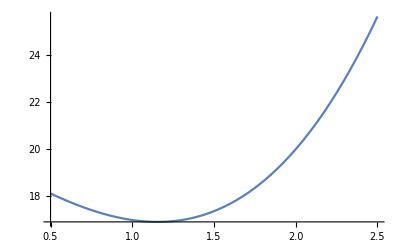

```mathematica
Plot[u1[x,at],{x,ax,bx}]
```

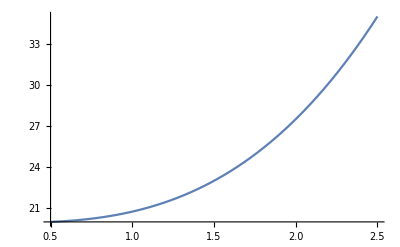

```mathematica
Plot[u1[x,bt],{x,ax,bx}]
```

Równanie przewodnictwa w fazie 1 (ciekłej)

```mathematica
a1*D[u1[x,t],{x,2}]-D[u1[x,t],t]
```

0

Równanie przewodnictwa w fazie 2 (stałej)

```mathematica
a2*D[u2[x,t],{x,2}]-D[u2[x,t],t]
```

0

Warunek początkowy

dla x ∈ [ax, 2]

```mathematica
u1[x,0]
```

20-4 x+x^3

dla x ∈ [2, bx]

```mathematica
u2[x,0]
```

16+x^2

Warunek brzegowy pierwszego rodzaju dla x=ax=0.5

```mathematica
u1[ax,t]
```

145/8+t/2

Warunek brzegowy pierwszego rodzaju dla x=bx=2.5

```mathematica
u2[bx,t]
```

89/4+t

Warunek ciągłości temperatury na granicy faz

```mathematica
u1[s[t],t]//Simplify
```

20

```mathematica
u2[s[t],t]//Simplify
```

20

Warunek Stefana

```mathematica
pl=Simplify[-λ1*(D[u1[x,t],x]/.{x->s[t]})]+λ2*(D[u2[x,t],x]/.{x->s[t]})
```

2 √(4-t)+4 (-4+t)

```mathematica
pp=D[s[t],t]
```

-1/(2 √(4-t))

```mathematica
pl/pp//FullSimplify
```

-4 (-1+2 √(4-t)) (-4+t)

```mathematica
kappa[t]*pp-pl//FullSimplify
```

0

### Pochodna Caputo po czasie, α=1/2

```mathematica
Clear[u1,u2,s,a1,a2,t,x,kappa,λ1,λ2,pl,pp];
```

```mathematica
u1[x_,t_]:=x^3+x*t-4*x+20;
u2[x_,t_]:=x^2+t+16;
s[t_]:=√(4-t)
```

```mathematica
a1=1/6;
a2=1/2;
λ1=2;
λ2=1;
tg=20;
```

Rząd pochodnej ułamkowej

```mathematica
α=1/2;
```

Obszar: x ∈ [0.5, 2.5], t ∈ [0, 15/4]

```mathematica
ax=1/2;
bx=5/2;
at=0;
bt=15/4;
```

```mathematica
Plot[u1[x,at],{x,ax,bx}]
```

-Graphics-

```mathematica
Plot[u1[x,bt],{x,ax,bx}]
```

-Graphics-

Równanie przewodnictwa w fazie 1 (ciekłej)

```mathematica
a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

x-(2 √t x)/(√π)

```mathematica
f1[x_,t_]:=-(x-(2 √t x)/(√π))
```

```mathematica
f1[x,t]+a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Równanie przewodnictwa w fazie 2 (stałej)

```mathematica
a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

1-(2 √t)/(√π)

```mathematica
f2[x_,t_]:=-(1-(2 √t)/(√π))
```

```mathematica
f2[x,t]+a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Warunek początkowy

dla x ∈ [ax, 2]

```mathematica
u1[x,0]
```

20-4 x+x^3

dla x ∈ [2, bx]

```mathematica
u2[x,0]
```

16+x^2

Warunek brzegowy pierwszego rodzaju dla x=ax=0.5

```mathematica
u1[ax,t]
```

145/8+t/2

Warunek brzegowy pierwszego rodzaju dla x=bx=2.5

```mathematica
u2[bx,t]
```

89/4+t

Warunek ciągłości temperatury na granicy faz

```mathematica
u1[s[t],t]//Simplify
```

20

```mathematica
u2[s[t],t]//Simplify
```

20

Warunek Stefana

```mathematica
pl=Simplify[-λ1*(D[u1[x,t],x]/.{x->s[t]})]+λ2*(D[u2[x,t],x]/.{x->s[t]})
```

2 √(4-t)+4 (-4+t)

```mathematica
pp=1/Gamma[1-α] Integrate[(D[s[t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(at<t<bt)]
```

-ArcCosh[2/(√(4-t))]/(√π)

```mathematica
kappaNew=pl/pp//FullSimplify
```

-(2 √π (-8+√(4-t)+2 t))/ArcCosh[2/(√(4-t))]

```mathematica
kappaNew*pp-pl//FullSimplify
```

0

```mathematica
Reduce[ArcCosh[2/(√(4-t))]==0,t]
```

t==0

### Pochodna Caputo po czasie, α=8/10

```mathematica
Clear[u1,u2,s,a1,a2,t,x,kappa,λ1,λ2,pl,pp];
```

```mathematica
u1[x_,t_]:=x^3+x*t-4*x+20;
u2[x_,t_]:=x^2+t+16;
s[t_]:=√(4-t)
```

```mathematica
a1=1/6;
a2=1/2;
λ1=2;
λ2=1;
tg=20;
```

Rząd pochodnej ułamkowej

```mathematica
α=8/10;
```

Obszar: x ∈ [0.5, 2.5], t ∈ [0, 15/4]

```mathematica
ax=1/2;
bx=5/2;
at=0;
bt=15/4;
```

Równanie przewodnictwa w fazie 1 (ciekłej)

```mathematica
a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

x-(5 t^(1/5) x)/Gamma[1/5]

```mathematica
f1[x_,t_]:=-(x-(5 t^(1/5) x)/Gamma[1/5])
```

```mathematica
f1[x,t]+a1*D[u1[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u1[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Równanie przewodnictwa w fazie 2 (stałej)

```mathematica
a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

1-(5 t^(1/5))/Gamma[1/5]

```mathematica
f2[x_,t_]:=-(1-(5 t^(1/5))/Gamma[1/5])
```

```mathematica
f2[x,t]+a2*D[u2[x,t],{x,2}]-1/Gamma[1-α] Integrate[(D[u2[x,t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(0≤t)]
```

0

Warunek początkowy

dla x ∈ [ax, 2]

```mathematica
u1[x,0]
```

20-4 x+x^3

dla x ∈ [2, bx]

```mathematica
u2[x,0]
```

16+x^2

Warunek brzegowy pierwszego rodzaju dla x=ax=0.5

```mathematica
u1[ax,t]
```

145/8+t/2

Warunek brzegowy pierwszego rodzaju dla x=bx=2.5

```mathematica
u2[bx,t]
```

89/4+t

Warunek ciągłości temperatury na granicy faz

```mathematica
u1[s[t],t]//Simplify
```

20

```mathematica
u2[s[t],t]//Simplify
```

20

Warunek Stefana

```mathematica
pl=Simplify[-λ1*(D[u1[x,t],x]/.{x->s[t]})]+λ2*(D[u2[x,t],x]/.{x->s[t]})
```

2 √(4-t)+4 (-4+t)

```mathematica
pp=1/Gamma[1-α] Integrate[(D[s[t],t]/.{t->s1})/(t-s1)^α,{s1,0,t},Assumptions->(at<t<bt)]
```

(5 (4 Hypergeometric2F1[-1/2,1,1/5,t/4]+(-4+t) Hypergeometric2F1[1/2,1,1/5,t/4]))/(16 t^(4/5) Gamma[1/5])

```mathematica
kappaNew=pl/pp//FullSimplify
```

(32 t^(4/5) (-8+√(4-t)+2 t) Gamma[1/5])/(5 (4 Hypergeometric2F1[-1/2,1,1/5,t/4]+(-4+t) Hypergeometric2F1[1/2,1,1/5,t/4]))

```mathematica
kappaNew*pp-pl//FullSimplify
```

0

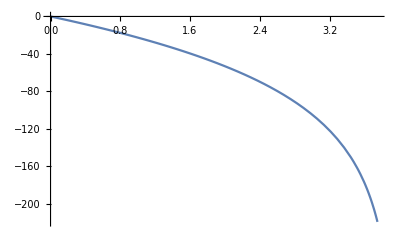

```mathematica
Plot[(5 (4 Hypergeometric2F1[-1/2,1,1/5,t/4]+(-4+t) Hypergeometric2F1[1/2,1,1/5,t/4])),{t,at,bt}]
```

```mathematica
(5 (4 Hypergeometric2F1[-1/2,1,1/5,t/4]+(-4+t) Hypergeometric2F1[1/2,1,1/5,t/4]))/.{t->at}
```

0